## Seasonal Ricker model - EWS in rb - Singles

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Google\ Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_seasonal"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=-0.2;
bh=1.2;
```

## Import Data

```mathematica
(* Name of simluation run *)
simName="trans_rb_tmax200";
```

```mathematica
(* Import EWS DataFrame *)
dfEws=Import["data_export/"<>simName<>"/ews_singles.csv"];
```

```mathematica
(* Import power spectrum DataFrame *)
dfPspec=Import["data_export/"<>simName<>"/pspec.csv"];
```

```mathematica
(* Import ews means DataFrame *)
dfEwsMeans=Import["data_export/"<>simName<>"/ews_means.csv"];
```

```mathematica
(* Import ews sd DataFrame *)
dfEwsSd=Import["data_export/"<>simName<>"/ews_deviations.csv"];
```

```mathematica
(* Import Kendall tau values *)
dfKtau=Import["data_export/"<>simName<>"/ktau.csv"];
```

```mathematica
numSims=Length[Union[dfEws[[2;;,1]]]]
```

5

```mathematica
(* Realisation number to display *)
displayNum=1;
```

## Figure params

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* Extract info *)
realNum=1;
seriesB = Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Breeding",_,_}][[;;,{3,4}]];
seriesNB = Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Non-breeding",_,_}][[;;,{3,4}]];
seriesTotal= Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Total",_,_}][[;;,{3,4}]];
```

```mathematica
(* Useful info *)
tVals=seriesB[[;;,1]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
realMax=Max[dfEws[[;;,1]]][[1]];
stateVals=Union[dfEws[[2;;,2]]];
```

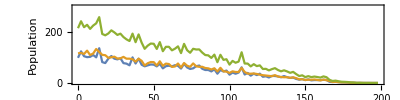

```mathematica
(* plot of breeding series *)
plotPop = ListPlot[{seriesB,seriesNB,seriesTotal},
Joined->True,
LabelStyle->12,
PlotLegends->Placed[trajLegend,Scaled[{0.85,0.7}]],
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Breeding growth rate, r_b"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
AxesLabel->{"t","Population"},
PlotRange->{{0,tmax},{0,300}}]
```

```mathematica
(* line legend *)
trajLegend=LineLegend[TMBcolours[[1;;3]],{"Breeding","Non-breeding","Total"},Spacings->{0,0.2},LabelStyle->10]
```

### Output

```mathematica
rTicks=Range[bl,bh,0.5];
rTicksT=(rTicks-bh)*tmax/(bl-bh);
```

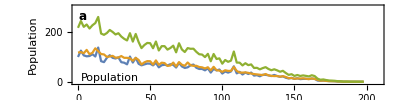

```mathematica
plotTraj=Show[{plotPop},
PlotRange->{{0,tmax*1.05},{-5,300}},
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Breeding growth rate, r_b"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{rTicksT,rTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Population",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}]}
]
```

## EWS Plots (Mean +/- SD)

### Variance

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Variance"][[1,1]];
```

```mathematica
ewsVals=Table[Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}],{state,stateVals}][[;;,;;,{3,4}]];
```

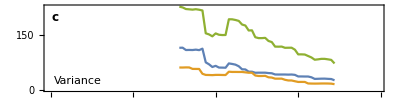

```mathematica
(* Plot EWS *)
plotVar=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Variance",ls],textPos,{-1,0}]}]
```

### Coefficient of variation

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
ewsVals=Table[Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}],{state,stateVals}][[;;,;;,{3,4}]];
```

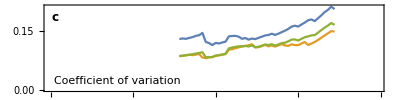

```mathematica
(* Plot EWS *)
plotCv=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}]
```

### Smax/Var

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Var"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

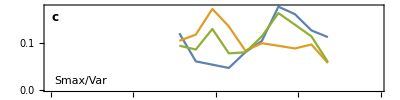

```mathematica
(* Plot EWS *)
plotSmaxVar=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Smax/Var",ls],textPos,{-1,0}]}]
```

### Skewness

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Skewness"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

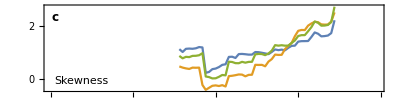

```mathematica
(* Plot EWS *)
plotSkew=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Skewness",ls],textPos,{-1,0}]}]
```

### Lag-1 AC

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

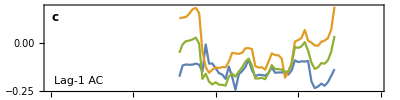

```mathematica
(* Plot EWS *)
plotAc1=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Lag-1 AC",ls],textPos,{-1,0}]}]
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

### Variance

```mathematica
indexKtau=Position[dfKtau[[1]],"Variance"][[1,1]]
```

7

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.913121 | -0.945035 | -0.973404 | -0.953901 | -0.95922 | -0.920213 | -0.804965 | -0.916667 | -0.955674 | -0.898936 | -0.932624 | -0.891844 | -0.98227 | -0.950355 | -0.897163 | -0.907801 | -0.920213 | -0.677305 | -0.868794 | -0.95922 | -0.943262 | -0.950355 | -0.840426 | -0.923759 | -0.874113 | -0.927305 | -0.888298 | -0.803191 | -0.966312 | -0.939716 | -0.710993 | -0.852837 | -0.937943 | -0.751773 | -0.968085 | -0.927305 | -0.945035 | -0.898936 | -0.875887 | -0.973404 | -0.906028 | -0.941489 | -0.929078 | -0.948582 | -0.945035 | -0.861702 | -0.952128 | -0.923759 | -0.939716 | -0.929078 | -0.89539 | -0.923759 | -0.960993 | -0.966312 | -0.971631 | -0.911348 | -0.904255 | -0.76773 | -0.939716 | -0.950355 | -0.994681 | -0.960993 | -0.921986 | -0.927305 | -0.829787 | -0.950355 | -0.54078 | -0.906028 | -0.946809 | -0.93617 | -0.95922 | -0.902482 | -0.943262 | -0.937943 | -0.941489 | -0.925532 | -0.937943 | -0.948582 | -0.964539 | -0.960993 | -0.840426 | -0.914894 | -0.952128 | -0.921986 | -0.955674 | -0.939716 | -0.718085 | -0.916667 | -0.941489 | -0.952128 | -0.973404 | -0.907801 | -0.943262 | -0.898936 | -0.93617 | -0.677305 | -0.87766 | -0.97695 | -0.952128 | -0.966312
Non-breeding | -0.824468 | -0.780142 | -0.925532 | -0.91844 | -0.927305 | -0.932624 | -0.916667 | -0.937943 | -0.964539 | -0.89539 | -0.875887 | -0.897163 | -0.968085 | -0.925532 | -0.927305 | -0.960993 | -0.916667 | -0.659574 | -0.441489 | -0.948582 | -0.960993 | -0.913121 | -0.914894 | -0.952128 | -0.909574 | -0.932624 | -0.930851 | -0.870567 | -0.911348 | -0.886525 | -0.716312 | -0.757092 | -0.906028 | -0.781915 | -0.960993 | -0.93617 | -0.921986 | -0.964539 | -0.909574 | -0.916667 | -0.916667 | -0.948582 | -0.712766 | -0.893617 | -0.941489 | -0.781915 | -0.930851 | -0.946809 | -0.941489 | -0.820922 | -0.946809 | -0.865248 | -0.87766 | -0.87766 | -0.93617 | -0.902482 | -0.934397 | -0.879433 | -0.414894 | -0.907801 | -0.946809 | -0.95922 | -0.897163 | -0.858156 | -0.886525 | -0.833333 | -0.812057 | -0.888298 | -0.909574 | -0.771277 | -0.960993 | -0.815603 | -0.95922 | -0.920213 | -0.95922 | -0.932624 | -0.900709 | -0.851064 | -0.937943 | -0.824468 | -0.927305 | -0.771277 | -0.875887 | -0.955674 | -0.778369 | -0.914894 | -0.932624 | -0.817376 | -0.953901 | -0.937943 | -0.994681 | -0.93617 | -0.820922 | -0.806738 | -0.897163 | -0.898936 | -0.893617 | -0.930851 | -0.950355 | -0.891844
Total | -0.856383 | -0.829787 | -0.95922 | -0.927305 | -0.939716 | -0.909574 | -0.810284 | -0.902482 | -0.950355 | -0.861702 | -0.900709 | -0.867021 | -0.941489 | -0.948582 | -0.904255 | -0.943262 | -0.904255 | -0.546099 | -0.533688 | -0.932624 | -0.955674 | -0.882979 | -0.838652 | -0.941489 | -0.836879 | -0.927305 | -0.822695 | -0.753546 | -0.925532 | -0.925532 | -0.620567 | -0.755319 | -0.884752 | -0.654255 | -0.978723 | -0.909574 | -0.897163 | -0.921986 | -0.836879 | -0.962766 | -0.900709 | -0.932624 | -0.83156 | -0.921986 | -0.934397 | -0.58156 | -0.962766 | -0.907801 | -0.907801 | -0.881206 | -0.934397 | -0.874113 | -0.897163 | -0.962766 | -0.946809 | -0.920213 | -0.937943 | -0.624113 | -0.845745 | -0.890071 | -0.968085 | -0.920213 | -0.941489 | -0.888298 | -0.875887 | -0.937943 | -0.512411 | -0.847518 | -0.907801 | -0.902482 | -0.941489 | -0.865248 | -0.952128 | -0.87766 | -0.957447 | -0.89539 | -0.89539 | -0.927305 | -0.953901 | -0.948582 | -0.923759 | -0.824468 | -0.91844 | -0.927305 | -0.893617 | -0.921986 | -0.884752 | -0.890071 | -0.948582 | -0.973404 | -0.971631 | -0.927305 | -0.875887 | -0.851064 | -0.886525 | -0.794326 | -0.792553 | -0.948582 | -0.962766 | -0.925532

```mathematica
(* Box plot *)
boxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Skewness

```mathematica
indexKtau=Position[dfKtau[[1]],"Skewness"][[1,1]]
```

11

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.58156 | 0.677305 | 0.274823 | 0.037234 | -0.365248 | 0.730496 | -0.0460993 | -0.375887 | -0.228723 | 0.514184 | 0.326241 | 0.164894 | 0.0195035 | -0.134752 | 0.379433 | 0.718085 | -0.308511 | 0.842199 | 0.367021 | 0.132979 | 0.0744681 | 0.503546 | 0.287234 | 0.402482 | 0.762411 | -0.365248 | 0.170213 | 0.296099 | -0.343972 | 0.661348 | 0.774823 | 0.345745 | -0.558511 | 0.679078 | 0.304965 | -0.632979 | 0.576241 | -0.304965 | 0.210993 | 0.315603 | -0.283688 | 0.198582 | -0.150709 | -0.0443262 | 0.125887 | -0.0407801 | 0.304965 | -0.0425532 | 0.328014 | 0.751773 | 0.852837 | 0.292553 | 0.161348 | 0.315603 | -0.264184 | -0.18617 | 0.826241 | 0.739362 | 0.260638 | 0.0407801 | 0.216312 | 0.0762411 | 0.531915 | -0.659574 | 0.234043 | 0.14539 | 0.411348 | 0.420213 | 0.661348 | -0.304965 | 0.427305 | -0.0921986 | -0.285461 | 0.427305 | -0.469858 | 0.700355 | -0.117021 | -0.0833333 | -0.20922 | 0.159574 | 0.466312 | 0.370567 | 0.62234 | 0.491135 | 0.351064 | 0.858156 | -0.352837 | 0.108156 | 0.398936 | -0.675532 | -0.193262 | 0.469858 | 0.37766 | -0.329787 | 0.340426 | 0.41844 | -0.175532 | 0.494681 | 0.556738 | -0.0567376
Non-breeding | 0.702128 | 0.336879 | 0.602837 | -0.358156 | -0.23227 | 0.234043 | 0.445035 | -0.583333 | 0.629433 | -0.356383 | 0.207447 | 0.828014 | -0.18617 | 0.443262 | 0.618794 | -0.597518 | -0.421986 | 0.593972 | 0.00177305 | 0.820922 | 0.52305 | 0.180851 | -0.171986 | -0.0230496 | -0.379433 | -0.397163 | -0.253546 | 0.512411 | -0.0212766 | 0.391844 | 0.106383 | 0.592199 | -0.251773 | 0.241135 | 0.510638 | 0.164894 | 0.202128 | 0.617021 | 0.448582 | 0.0549645 | -0.22695 | -0.102837 | 0.223404 | 0.489362 | 0.551418 | 0.317376 | 0.25 | -0.342199 | 0.297872 | 0.849291 | 0.776596 | 0.783688 | 0.620567 | 0.804965 | -0.650709 | 0.608156 | 0.593972 | -0.347518 | 0.285461 | -0.539007 | 0.163121 | 0.684397 | -0.12766 | -0.636525 | 0.698582 | 0.801418 | 0.558511 | 0.693262 | 0.879433 | -0.661348 | -0.501773 | -0.684397 | 0.391844 | 0.173759 | -0.223404 | 0.219858 | -0.0744681 | 0.680851 | -0.0336879 | -0.289007 | 0.320922 | 0.710993 | -0.00177305 | 0.710993 | 0.691489 | 0.16844 | 0.689716 | 0.531915 | -0.251773 | -0.317376 | 0.0691489 | 0.326241 | 0.0780142 | -0.253546 | 0.576241 | -0.202128 | -0.177305 | 0.687943 | 0.329787 | -0.0443262
Total | 0.702128 | 0.547872 | 0.347518 | -0.33156 | -0.297872 | 0.565603 | 0.37766 | -0.262411 | -0.18617 | 0.652482 | 0.328014 | 0.842199 | 0.0070922 | 0.0957447 | 0.567376 | 0.390071 | -0.437943 | 0.824468 | -0.455674 | 0.414894 | 0.496454 | 0.515957 | 0.070922 | 0.37766 | 0.526596 | -0.386525 | 0.136525 | 0.414894 | -0.427305 | 0.547872 | 0.432624 | 0.202128 | -0.512411 | 0.489362 | 0.546099 | -0.347518 | 0.570922 | -0.33156 | -0.0549645 | 0.072695 | -0.198582 | 0.161348 | -0.166667 | 0.184397 | 0.163121 | -0.393617 | 0.0549645 | 0.12766 | 0.289007 | 0.824468 | 0.867021 | 0.52305 | 0.0904255 | 0.859929 | -0.432624 | 0.519504 | 0.556738 | 0.757092 | 0.492908 | -0.301418 | 0.184397 | 0.393617 | 0.35461 | -0.404255 | 0.460993 | 0.450355 | 0.679078 | 0.457447 | 0.801418 | -0.326241 | -0.207447 | -0.345745 | -0.109929 | 0.51773 | -0.505319 | 0.280142 | -0.182624 | 0.0851064 | -0.184397 | -0.132979 | 0.466312 | 0.565603 | 0.0797872 | 0.453901 | 0.265957 | 0.780142 | -0.0283688 | 0.671986 | 0.237589 | -0.634752 | -0.134752 | 0.421986 | 0.560284 | -0.586879 | 0.521277 | 0.388298 | -0.228723 | 0.597518 | 0.471631 | 0.214539

```mathematica
(* Box plot *)
boxSkew=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Coefficient of variation

```mathematica
indexKtau=Position[dfKtau[[1]],"Coefficient of variation"][[1,1]]
```

4

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.707447 | 0.677305 | 0.102837 | 0.5 | 0.801418 | 0.702128 | 0.491135 | 0.329787 | 0.0425532 | 0.906028 | 0.671986 | 0.677305 | -0.489362 | 0.650709 | 0.796099 | 0.762411 | 0.539007 | 0.890071 | 0.874113 | 0.148936 | 0.744681 | 0.304965 | 0.881206 | 0.808511 | 0.939716 | 0.508865 | 0.654255 | 0.258865 | 0.140071 | 0.941489 | 0.945035 | 0.870567 | 0.858156 | 0.868794 | -0.0141844 | 0.652482 | 0.884752 | 0.510638 | 0.902482 | 0.51773 | 0.836879 | 0.0070922 | 0.663121 | 0.687943 | 0.599291 | 0.787234 | 0.0921986 | 0.882979 | 0.102837 | 0.565603 | 0.863475 | 0.707447 | 0.26773 | 0.579787 | 0.574468 | 0.757092 | 0.840426 | 0.953901 | 0.430851 | 0.87234 | 0.191489 | 0.469858 | 0.297872 | 0.734043 | 0.909574 | 0.393617 | 0.980496 | 0.760638 | 0.710993 | 0.808511 | -0.299645 | 0.829787 | 0.796099 | 0.863475 | 0.836879 | 0.897163 | 0.324468 | 0.689716 | 0.535461 | -0.0177305 | 0.735816 | 0.890071 | 0.66844 | 0.764184 | 0.845745 | 0.916667 | 0.900709 | 0.847518 | 0.792553 | 0.257092 | 0.462766 | 0.826241 | 0.742908 | 0.615248 | 0.755319 | 0.840426 | 0.778369 | 0.16844 | 0.453901 | 0.632979
Non-breeding | 0.804965 | 0.762411 | 0.875887 | 0.79078 | 0.911348 | 0.81383 | 0.640071 | 0.613475 | 0.475177 | 0.921986 | 0.792553 | 0.930851 | 0.606383 | 0.913121 | 0.797872 | 0.865248 | 0.661348 | 0.939716 | 0.966312 | 0.921986 | 0.641844 | 0.792553 | 0.955674 | 0.957447 | 0.913121 | 0.687943 | 0.836879 | 0.663121 | 0.851064 | 0.923759 | 0.932624 | 0.707447 | 0.955674 | 0.852837 | 0.365248 | 0.705674 | 0.921986 | 0.673759 | 0.904255 | 0.851064 | 0.913121 | 0.893617 | 0.925532 | 0.838652 | 0.549645 | 0.957447 | 0.760638 | 0.934397 | 0.455674 | 0.815603 | 0.725177 | 0.829787 | 0.946809 | 0.941489 | 0.774823 | 0.881206 | 0.91844 | 0.968085 | 0.867021 | 0.930851 | 0.579787 | 0.838652 | 0.744681 | 0.927305 | 0.890071 | 0.957447 | 0.929078 | 0.937943 | 0.913121 | 0.757092 | 0.742908 | 0.888298 | 0.567376 | 0.882979 | 0.909574 | 0.950355 | 0.879433 | 0.923759 | 0.606383 | 0.879433 | 0.85461 | 0.960993 | 0.966312 | 0.842199 | 0.948582 | 0.898936 | 0.906028 | 0.845745 | 0.804965 | 0.68617 | 0.0744681 | 0.950355 | 0.87766 | 0.904255 | 0.663121 | 0.934397 | 0.87234 | 0.741135 | 0.785461 | 0.937943
Total | 0.879433 | 0.72695 | 0.75 | 0.843972 | 0.890071 | 0.780142 | 0.546099 | 0.501773 | 0.382979 | 0.971631 | 0.73227 | 0.836879 | -0.202128 | 0.856383 | 0.812057 | 0.863475 | 0.602837 | 0.964539 | 0.946809 | 0.471631 | 0.819149 | 0.714539 | 0.932624 | 0.921986 | 0.925532 | 0.737589 | 0.828014 | 0.485816 | 0.39539 | 0.921986 | 0.952128 | 0.774823 | 0.939716 | 0.868794 | 0.0939716 | 0.710993 | 0.921986 | 0.66844 | 0.906028 | 0.787234 | 0.902482 | 0.698582 | 0.828014 | 0.865248 | 0.496454 | 0.904255 | 0.595745 | 0.932624 | 0.411348 | 0.781915 | 0.845745 | 0.863475 | 0.840426 | 0.911348 | 0.746454 | 0.852837 | 0.863475 | 0.975177 | 0.656028 | 0.948582 | 0.333333 | 0.739362 | 0.531915 | 0.916667 | 0.93617 | 0.769504 | 0.969858 | 0.897163 | 0.85461 | 0.716312 | 0.308511 | 0.890071 | 0.730496 | 0.865248 | 0.943262 | 0.927305 | 0.794326 | 0.840426 | 0.592199 | 0.81383 | 0.865248 | 0.95922 | 0.906028 | 0.884752 | 0.934397 | 0.932624 | 0.909574 | 0.865248 | 0.911348 | 0.624113 | 0.113475 | 0.934397 | 0.829787 | 0.746454 | 0.719858 | 0.925532 | 0.851064 | 0.487589 | 0.739362 | 0.812057

```mathematica
(* Box plot *)
boxCv=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax"][[1,1]]
```

12

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.155556 | -0.733333 | -0.911111 | -0.955556 | -0.644444 | -0.2 | -0.644444 | -0.866667 | -0.911111 | -0.822222 | -0.6 | -0.777778 | -0.911111 | -0.822222 | -0.777778 | -0.911111 | -0.955556 | -0.555556 | -0.333333 | -0.244444 | -0.911111 | -1. | -0.6 | -0.555556 | -0.777778 | -1. | -0.6 | -0.377778 | -0.777778 | -0.422222 | -0.288889 | -0.377778 | -0.733333 | -0.377778 | -0.911111 | -0.644444 | -0.688889 | -0.466667 | -0.688889 | -0.866667 | -0.6 | -0.955556 | -0.377778 | -0.866667 | -0.866667 | 0.377778 | -0.777778 | -0.822222 | -0.822222 | -0.466667 | -0.777778 | -0.911111 | -0.955556 | -0.822222 | -0.866667 | -0.288889 | -0.777778 | 0.2 | -0.466667 | -0.688889 | -0.866667 | -0.644444 | -0.822222 | -0.911111 | -0.733333 | -0.644444 | 0.2 | -0.6 | -0.511111 | -0.6 | -1. | 0.111111 | -0.644444 | -0.333333 | -0.866667 | -0.688889 | -0.866667 | -0.644444 | -0.911111 | -0.955556 | -0.733333 | -0.511111 | -0.777778 | -0.955556 | -0.511111 | -0.6 | -0.866667 | -0.644444 | -0.955556 | -1. | -0.733333 | -0.911111 | -0.777778 | -0.644444 | -0.688889 | -0.733333 | -0.733333 | -0.644444 | -0.955556 | -0.777778
Non-breeding | -0.822222 | -0.511111 | -0.955556 | -0.955556 | -0.422222 | -0.466667 | -0.822222 | -0.6 | -0.511111 | -0.244444 | 0.244444 | -0.866667 | -0.866667 | -0.822222 | -0.822222 | -0.511111 | -0.777778 | 0.688889 | 0.2 | -0.644444 | -0.911111 | -0.955556 | -0.644444 | -0.244444 | -0.422222 | -0.822222 | -0.644444 | -0.377778 | -0.822222 | -0.244444 | -0.377778 | -0.288889 | -0.377778 | -0.644444 | -0.866667 | -0.822222 | -0.777778 | -0.555556 | -0.466667 | -0.466667 | -0.644444 | -0.866667 | -0.111111 | -0.866667 | -0.822222 | 0.0666667 | -0.288889 | -0.644444 | -0.822222 | -0.911111 | -1. | -0.377778 | -0.777778 | -0.511111 | -0.866667 | -0.244444 | -0.777778 | -0.333333 | -0.0666667 | -0.555556 | -0.955556 | -0.733333 | -0.866667 | -0.822222 | -0.466667 | -0.333333 | -0.288889 | -0.644444 | -0.644444 | -0.0222222 | -0.733333 | 0.0666667 | -0.511111 | -0.866667 | -0.733333 | -0.466667 | -0.866667 | -0.822222 | -1. | -0.866667 | -1. | -0.244444 | -0.155556 | -0.466667 | -0.555556 | -0.6 | -0.466667 | -0.777778 | -0.422222 | -0.733333 | -0.911111 | -0.6 | -0.777778 | -0.688889 | -0.511111 | -0.377778 | 0.2 | -0.688889 | -0.777778 | -0.466667
Total | -0.555556 | -0.6 | -1. | -0.866667 | -0.555556 | -0.155556 | -0.644444 | -0.777778 | -0.644444 | -0.422222 | -0.377778 | -0.911111 | -0.866667 | -0.6 | -0.777778 | -0.644444 | -0.911111 | -0.0666667 | 0.155556 | -0.2 | -0.911111 | -0.955556 | -0.111111 | -0.155556 | -0.688889 | -0.822222 | -0.466667 | -0.466667 | -0.688889 | -0.111111 | -0.422222 | -0.155556 | -0.422222 | -0.688889 | -0.955556 | -0.733333 | -0.511111 | -0.422222 | -0.244444 | -0.644444 | -0.466667 | -0.866667 | 0.0222222 | -0.688889 | -0.822222 | 0.555556 | -0.511111 | -0.822222 | -0.688889 | -0.822222 | -0.777778 | -0.822222 | -0.822222 | -0.644444 | -0.866667 | -0.2 | -0.777778 | 0.422222 | -0.333333 | -0.6 | -0.777778 | -0.555556 | -0.866667 | -0.777778 | -0.244444 | -0.6 | 0.155556 | -0.466667 | -0.822222 | 0.0666667 | -0.911111 | 0.422222 | -0.466667 | -0.466667 | -0.777778 | -0.377778 | -0.866667 | -0.866667 | -1. | -0.911111 | -0.733333 | -0.333333 | -0.511111 | -0.955556 | -0.466667 | -0.644444 | -0.511111 | -0.733333 | -0.777778 | -0.866667 | -0.822222 | -0.644444 | -0.733333 | -0.6 | -0.6 | -0.466667 | -0.244444 | -0.688889 | -0.866667 | -0.555556

```mathematica
(* Box plot *)
boxSmax=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax/Var

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax/Var"][[1,1]]
```

9

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.333333 | -0.155556 | -0.244444 | -0.466667 | -0.0666667 | 0.466667 | 0.377778 | -0.244444 | 0.511111 | -0.6 | 0.288889 | -0.155556 | -0.244444 | 0.6 | -0.466667 | -0.2 | -0.6 | 0.0222222 | 0.0666667 | 0.288889 | -0.0222222 | -0.377778 | 0.111111 | 0.288889 | -0.0666667 | -0.466667 | -0.155556 | 0.466667 | 0.377778 | 0.511111 | 0.0666667 | 0.2 | -0.111111 | 0.0222222 | -0.333333 | 0.155556 | -0.111111 | -0.2 | 0.111111 | 0.244444 | 0.155556 | -0.511111 | 0.466667 | 0.244444 | 0.288889 | 0.777778 | 0.0666667 | -0.288889 | -0.333333 | 0.555556 | -0.333333 | -0.155556 | -0.466667 | 0.377778 | 0.2 | 0.333333 | 0.111111 | 0.6 | -0.0222222 | -0.111111 | -0.111111 | 0.0666667 | -0.244444 | -0.0666667 | 0.333333 | 0.333333 | 0.466667 | -0.2 | 0.6 | 0.244444 | -0.422222 | 0.822222 | 0.2 | 0.466667 | -0.244444 | 0.6 | 0.0222222 | -0.2 | 0.0666667 | 0.0222222 | -0.555556 | 0.288889 | 0.0222222 | -0.822222 | 0.333333 | 0.155556 | -0.288889 | 0.333333 | -0.511111 | -0.511111 | 0.244444 | -0.111111 | -0.155556 | -0.155556 | -0.155556 | -0.155556 | 0.555556 | 0.511111 | -0.155556 | 0.155556
Non-breeding | -0.511111 | -0.0666667 | 0.244444 | -0.111111 | -0.0666667 | 0.333333 | 0.0666667 | -0.2 | 0.377778 | 0.0222222 | 0.866667 | -0.555556 | -0.466667 | 0.644444 | 0.111111 | 0.333333 | -0.288889 | 0.777778 | 0.377778 | 0.0222222 | 0.0666667 | -0.2 | 0.288889 | 0.333333 | -0.0666667 | 0.2 | 0.288889 | 0.111111 | 0.0666667 | 0.466667 | 0.333333 | 0.6 | -0.155556 | -0.333333 | -0.244444 | 0.155556 | -0.2 | 0.155556 | 0.555556 | 0.0666667 | 0.111111 | -0.555556 | 0.0222222 | -0.2 | 0.644444 | 0.733333 | 0.244444 | -0.0222222 | 0.2 | -0.333333 | -0.0666667 | 0.422222 | -0.244444 | 0.2 | -0.0666667 | 0.333333 | -0.288889 | 0.422222 | 0.2 | 0.0222222 | -0.688889 | 0.377778 | -0.2 | 0.244444 | 0.466667 | 0.555556 | 0.155556 | -0.111111 | 0.155556 | 0.333333 | -0.244444 | 0.511111 | 0.0222222 | 0.866667 | 0.155556 | 0.466667 | -0.377778 | -0.288889 | 0.0666667 | -0.244444 | 0.288889 | 0.244444 | 0.422222 | 0.111111 | 0.288889 | 0.422222 | 0.288889 | 0.155556 | 0.644444 | 0.0222222 | 0.2 | 0.111111 | -0.111111 | -0.244444 | -0.111111 | 0.244444 | 0.688889 | 0.688889 | -0.111111 | 0.288889
Total | 0.0222222 | -0.111111 | -0.155556 | 0.777778 | -0.0666667 | 0.511111 | 0.244444 | -0.244444 | 0.333333 | -0.288889 | 0.866667 | -0.333333 | -0.466667 | 0.555556 | -0.244444 | 0.155556 | -0.6 | 0.288889 | 0.244444 | 0.244444 | 0.244444 | -0.111111 | 0.377778 | 0.422222 | -0.0222222 | 0.0666667 | 0.0666667 | 0.377778 | 0.377778 | 0.555556 | 0.0666667 | 0.422222 | -0.244444 | -0.333333 | -0.111111 | 0.2 | -0.0222222 | -0.155556 | 0.333333 | 0.111111 | 0.244444 | -0.333333 | 0.422222 | 0.0666667 | 0.288889 | 0.777778 | 0.0222222 | 0.111111 | 0.0666667 | -0.0222222 | -0.155556 | -0.155556 | -0.333333 | 0.422222 | 0.111111 | 0.333333 | -0.0222222 | 0.688889 | 0.111111 | -0.2 | -0.333333 | 0.244444 | -0.511111 | 0.0666667 | 0.688889 | 0.377778 | 0.333333 | -0.155556 | 0.688889 | 0.511111 | -0.155556 | 0.733333 | 0.2 | 0.688889 | 0.111111 | 0.377778 | -0.155556 | -0.422222 | -0.0222222 | -0.0666667 | -0.244444 | 0.0666667 | 0.377778 | -0.2 | 0.333333 | 0.422222 | -0.0222222 | 0.111111 | 0.511111 | -0.244444 | 0.333333 | -0.155556 | 0.0222222 | -0.111111 | -0.0666667 | 0.0666667 | 0.777778 | 0.555556 | -0.0666667 | 0.244444

```mathematica
(* Box plot *)
boxSmaxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-1 Autocorrelation

```mathematica
indexKtau=Position[dfKtau[[1]],"Lag-1 AC"][[1,1]]
```

13

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.191489 | 0.0673759 | 0.12234 | 0.771277 | 0.675532 | 0.76773 | 0.875887 | 0.927305 | 0.794326 | -0.037234 | 0.796099 | 0.430851 | 0.471631 | -0.0939716 | -0.342199 | 0.806738 | 0.0762411 | 0.863475 | 0.751773 | 0.434397 | 0.882979 | 0.562057 | 0.911348 | 0.75 | 0.891844 | -0.338652 | 0.48227 | 0.487589 | 0.455674 | 0.576241 | 0.879433 | -0.379433 | 0.562057 | 0.852837 | -0.244681 | 0.507092 | 0.468085 | 0.570922 | 0.618794 | 0.806738 | 0.641844 | 0.794326 | 0.83156 | 0.62766 | -0.223404 | 0.881206 | 0.180851 | 0.796099 | 0.457447 | 0.785461 | 0.578014 | 0.824468 | -0.725177 | 0.829787 | 0.521277 | 0.39539 | 0.666667 | 0.83156 | 0.695035 | 0.234043 | 0.716312 | 0.611702 | 0.437943 | 0.735816 | 0.554965 | 0.54078 | 0.810284 | 0.817376 | 0.762411 | 0.799645 | 0.0159574 | 0.670213 | 0.340426 | 0.631206 | 0.787234 | 0.340426 | 0.430851 | -0.0301418 | -0.129433 | 0.72695 | -0.301418 | 0.81383 | 0.778369 | -0.301418 | 0.359929 | 0.870567 | 0.554965 | 0.852837 | 0.382979 | 0.631206 | 0.615248 | 0.180851 | 0.746454 | -0.175532 | -0.271277 | -0.23227 | 0.836879 | 0.806738 | 0.397163 | 0.789007
Non-breeding | 0.117021 | -0.370567 | 0.551418 | 0.79078 | 0.789007 | 0.446809 | 0.776596 | 0.87766 | 0.684397 | 0.842199 | 0.939716 | 0.794326 | 0.684397 | 0.632979 | 0.526596 | 0.836879 | -0.519504 | 0.937943 | -0.406028 | 0.492908 | 0.801418 | 0.675532 | -0.111702 | 0.785461 | 0.913121 | 0.343972 | 0.359929 | 0.712766 | 0.565603 | 0.76773 | 0.741135 | 0.714539 | 0.363475 | 0.498227 | -0.308511 | 0.505319 | -0.530142 | 0.475177 | 0.60461 | 0.789007 | 0.840426 | 0.799645 | 0.897163 | 0.0992908 | 0.725177 | 0.879433 | 0.368794 | 0.728723 | 0.677305 | 0.797872 | 0.37766 | 0.586879 | 0.588652 | 0.81383 | 0.425532 | 0.221631 | 0.721631 | 0.836879 | 0.484043 | 0.599291 | 0.278369 | 0.705674 | -0.359929 | 0.781915 | 0.723404 | 0.751773 | 0.778369 | 0.781915 | 0.728723 | 0.893617 | 0.66844 | 0.714539 | 0.585106 | 0.73227 | 0.0301418 | 0.897163 | 0.781915 | 0.489362 | 0.546099 | 0.562057 | 0.519504 | 0.934397 | 0.911348 | 0.728723 | 0.808511 | 0.796099 | 0.858156 | 0.849291 | 0.822695 | 0.166667 | 0.425532 | 0.87234 | 0.407801 | 0.73227 | -0.0815603 | 0.620567 | 0.797872 | 0.632979 | 0.150709 | 0.769504
Total | 0.195035 | -0.124113 | 0.432624 | 0.757092 | 0.769504 | 0.624113 | 0.845745 | 0.91844 | 0.781915 | 0.558511 | 0.893617 | 0.677305 | 0.606383 | 0.264184 | -0.0141844 | 0.822695 | -0.359929 | 0.921986 | 0.301418 | 0.710993 | 0.856383 | 0.712766 | 0.781915 | 0.81383 | 0.927305 | 0.170213 | 0.609929 | 0.746454 | 0.530142 | 0.835106 | 0.884752 | 0.246454 | 0.597518 | 0.748227 | -0.333333 | 0.507092 | -0.0319149 | 0.547872 | 0.661348 | 0.808511 | 0.677305 | 0.835106 | 0.89539 | 0.501773 | 0.315603 | 0.874113 | 0.287234 | 0.804965 | 0.700355 | 0.780142 | 0.719858 | 0.828014 | 0.0301418 | 0.886525 | 0.551418 | 0.430851 | 0.787234 | 0.833333 | 0.680851 | 0.445035 | 0.705674 | 0.656028 | 0.109929 | 0.783688 | 0.810284 | 0.576241 | 0.888298 | 0.847518 | 0.742908 | 0.932624 | 0.423759 | 0.744681 | 0.404255 | 0.824468 | 0.70922 | 0.737589 | 0.640071 | -0.0407801 | -0.0283688 | 0.824468 | 0.0549645 | 0.904255 | 0.843972 | 0.285461 | 0.664894 | 0.87234 | 0.710993 | 0.85461 | 0.689716 | 0.640071 | 0.624113 | 0.778369 | 0.73227 | 0.315603 | -0.0656028 | 0.51773 | 0.824468 | 0.810284 | 0.315603 | 0.792553

```mathematica
(* Box plot *)
boxAc1=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

## Power Spectrum Plot

### Colour function

```mathematica
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Organise power spectrum data

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[dfPspec[[2;;,3]]][[1;;-1;;8]]
```

{78.,158.}

```mathematica
dfPspec[[1]]
```

{Realisation number,Variable,Time,Frequency,Empirical}

```mathematica
(* Power spectra of display plot *)
specData=Table[
Cases[dfPspec,{displayNum,"Total",timeVal,_,_}][[;;,{4,5}]],
{timeVal,plotTimes}];
```

```mathematica
(* Power spectra normalised by the variance *)
varianceVals=Table[Cases[dfEws[[2;;,{1,2,3,8}]],{displayNum,"Total",Round[time],_}][[1,4]],{time,plotTimes}];
specNormData=specData;
specNormData[[;;,;;,2]]=specNormData[[;;,;;,2]]/varianceVals;
```

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

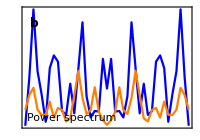

```mathematica
plotPspec=ListLinePlot[specData,
PlotRange->All,
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Automatic},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

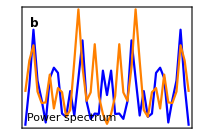

```mathematica
plotPspecNorm=ListLinePlot[specNormData,
PlotRange->All,
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Automatic},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.2cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.5cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+4*heightEws+heightBif+4*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotAc1,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxAc1,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotSmaxVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSmaxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotCv,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxCv,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th (top) row  *)
Inset[Show[plotTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspecNorm,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

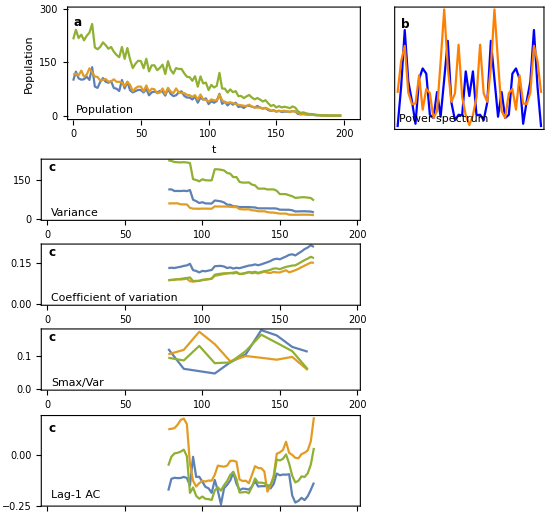

```mathematica
plotGrid
```

```mathematica
Export["figures/singles_"<>simName<>".png",plotGrid,ImageResolution->200];
```